```mathematica
(* between the two Quit[] is kind of draft i used to calculate the coefficients of the polynomials for weno3 interpolation.  details are available in the methodology session at: http://lsec.cc.ac.cn/lcfd/WENO_mem.html *)
```

```mathematica
(* funciton u[x] next to the second Quit[] is the test function i used to verify the coefficients computed by the weno3 scheme above *)
```

```mathematica
Quit[]
```

```mathematica
AA[k_]=Table[1/j((k+i+1/2)^j-(k+i-1/2)^j),{i,-1,1},{j,1,3}];
AA[-1]//Simplify//MatrixForm
```

(1 | -2 | 49/12
1 | -1 | 13/12
1 | 0 | 1/12)

```mathematica
({{1, 1/2, (1/2)^2}}).Inverse[({{1, -2, 49/12}, {1, -1, 13/12}, {1, 0, 1/12}})].({{Subscript[u, -2]}, {Subscript[u, -1]}, {Subscript[u, 0]}})//Simplify//MatrixForm
({{1, -1/2, (-1/2)^2}}).Inverse[({{1, -2, 49/12}, {1, -1, 13/12}, {1, 0, 1/12}})].({{Subscript[u, -2]}, {Subscript[u, -1]}, {Subscript[u, 0]}})//Simplify//MatrixForm
```

(1/6 (2 u_-2-7 u_-1+11 u_0))

(1/6 (-u_-2+5 u_-1+2 u_0))

```mathematica
Inverse[({{1, -2, 49/12}, {1, -1, 13/12}, {1, 0, 1/12}})].({{Subscript[u, -2]}, {Subscript[u, -1]}, {Subscript[u, 0]}})//Simplify//MatrixForm
```

(1/24 (-u_-2+2 u_-1+23 u_0)
1/2 (u_-2-4 u_-1+3 u_0)
1/2 (u_-2-2 u_-1+u_0))

```mathematica
AA[0]//Simplify//MatrixForm
```

(1 | -1 | 13/12
1 | 0 | 1/12
1 | 1 | 13/12)

```mathematica
({{1, 1/2, (1/2)^2}}).Inverse[({{1, -1, 13/12}, {1, 0, 1/12}, {1, 1, 13/12}})].({{Subscript[u, -1]}, {Subscript[u, 0]}, {Subscript[u, 1]}})//Simplify//MatrixForm
({{1, -1/2, (-1/2)^2}}).Inverse[({{1, -1, 13/12}, {1, 0, 1/12}, {1, 1, 13/12}})].({{Subscript[u, -1]}, {Subscript[u, 0]}, {Subscript[u, 1]}})//Simplify//MatrixForm
```

(1/6 (-u_-1+5 u_0+2 u_1))

(1/6 (2 u_-1+5 u_0-u_1))

```mathematica
Inverse[({{1, -1, 13/12}, {1, 0, 1/12}, {1, 1, 13/12}})].({{Subscript[u, -1]}, {Subscript[u, 0]}, {Subscript[u, 1]}})//Simplify//MatrixForm
```

(1/24 (-u_-1+26 u_0-u_1)
1/2 (-u_-1+u_1)
1/2 (u_-1-2 u_0+u_1))

```mathematica
AA[+1]//Simplify//MatrixForm
```

(1 | 0 | 1/12
1 | 1 | 13/12
1 | 2 | 49/12)

```mathematica
({{1, 1/2, (1/2)^2}}).Inverse[({{1, 0, 1/12}, {1, 1, 13/12}, {1, 2, 49/12}})].({{Subscript[u, 0]}, {Subscript[u, 1]}, {Subscript[u, 2]}})//Simplify//MatrixForm
({{1, -1/2, (-1/2)^2}}).Inverse[({{1, 0, 1/12}, {1, 1, 13/12}, {1, 2, 49/12}})].({{Subscript[u, 0]}, {Subscript[u, 1]}, {Subscript[u, 2]}})//Simplify//MatrixForm
```

(1/6 (2 u_0+5 u_1-u_2))

(1/6 (11 u_0-7 u_1+2 u_2))

```mathematica
Inverse[({{1, 0, 1/12}, {1, 1, 13/12}, {1, 2, 49/12}})].({{Subscript[u, 0]}, {Subscript[u, 1]}, {Subscript[u, 2]}})//Simplify//MatrixForm
```

(1/24 (23 u_0+2 u_1-u_2)
1/2 (-3 u_0+4 u_1-u_2)
1/2 (u_0-2 u_1+u_2))

```mathematica
BB[k_]=Table[1/j((k+i+1/2)^j-(k+i-1/2)^j),{i,-2,2},{j,1,5}];
BB[0]//Simplify//MatrixForm
```

(1 | -2 | 49/12 | -17/2 | 1441/80
1 | -1 | 13/12 | -5/4 | 121/80
1 | 0 | 1/12 | 0 | 1/80
1 | 1 | 13/12 | 5/4 | 121/80
1 | 2 | 49/12 | 17/2 | 1441/80)

```mathematica
({{1, 1/2, (1/2)^2, (1/2)^3, (1/2)^4}}).Inverse[({{1, -2, 49/12, -17/2, 1441/80}, {1, -1, 13/12, -5/4, 121/80}, {1, 0, 1/12, 0, 1/80}, {1, 1, 13/12, 5/4, 121/80}, {1, 2, 49/12, 17/2, 1441/80}})].({{Subscript[u, -2]}, {Subscript[u, -1]}, {Subscript[u, 0]}, {Subscript[u, 1]}, {Subscript[u, 2]}})//Simplify//MatrixForm
({{1, -1/2, (-1/2)^2, (-1/2)^3, (-1/2)^4}}).Inverse[({{1, -2, 49/12, -17/2, 1441/80}, {1, -1, 13/12, -5/4, 121/80}, {1, 0, 1/12, 0, 1/80}, {1, 1, 13/12, 5/4, 121/80}, {1, 2, 49/12, 17/2, 1441/80}})].({{Subscript[u, -2]}, {Subscript[u, -1]}, {Subscript[u, 0]}, {Subscript[u, 1]}, {Subscript[u, 2]}})//Simplify//MatrixForm
```

(1/60 (2 u_-2-13 u_-1+47 u_0+27 u_1-3 u_2))

(1/60 (-3 u_-2+27 u_-1+47 u_0-13 u_1+2 u_2))

```mathematica
Inverse[({{1, -2, 49/12, -17/2, 1441/80}, {1, -1, 13/12, -5/4, 121/80}, {1, 0, 1/12, 0, 1/80}, {1, 1, 13/12, 5/4, 121/80}, {1, 2, 49/12, 17/2, 1441/80}})].({{Subscript[u, -2]}, {Subscript[u, -1]}, {Subscript[u, 0]}, {Subscript[u, 1]}, {Subscript[u, 2]}})//Simplify//MatrixForm
```

((9 u_-2-116 u_-1+2134 u_0-116 u_1+9 u_2)/1920
1/48 (5 u_-2-34 u_-1+34 u_1-5 u_2)
1/16 (-u_-2+12 u_-1-22 u_0+12 u_1-u_2)
1/12 (-u_-2+2 u_-1-2 u_1+u_2)
1/24 (u_-2-4 u_-1+6 u_0-4 u_1+u_2))

```mathematica
Quit[]
```

```mathematica
u[x_]=If[x<0.2,0,If[x≤0.8,(x-0.2)^3-0.4^3,0]];
```

```mathematica
p0[x_]=Inverse[({{1, -2, 49/12}, {1, -1, 13/12}, {1, 0, 1/12}})].({{u[(x-2) dx]}, {u[(x-1) dx]}, {u[x dx]}});
p1[x_]=Inverse[({{1, -1, 13/12}, {1, 0, 1/12}, {1, 1, 13/12}})].({{u[(x-1) dx]}, {u[x dx]}, {u[(x+1) dx]}});
p2[x_]=Inverse[({{1, 0, 1/12}, {1, 1, 13/12}, {1, 2, 49/12}})].({{u[x dx]}, {u[(x+1) dx]}, {u[(x+2) dx]}});
```

```mathematica
pf0[x_,y_]=({{1, x, x^2}}).p0[y];
pf1[x_,y_]=({{1, x, x^2}}).p1[y];
pf2[x_,y_]=({{1, x, x^2}}).p2[y];
```

```mathematica
b0[x_]=13/3(p0[x][[3,1]])^2+(p0[x][[2,1]])^2;
b1[x_]=13/3(p1[x][[3,1]])^2+(p1[x][[2,1]])^2;
b2[x_]=13/3(p2[x][[3,1]])^2+(p2[x][[2,1]])^2;
```

```mathematica
wm[i_]=(1/10)/(b0[i]+ϵ)^2+(6/10)/(b1[i]+ϵ)^2+(3/10)/(b2[i]+ϵ)^2;
wp[i_]=(3/10)/(b0[i]+ϵ)^2+(6/10)/(b1[i]+ϵ)^2+(1/10)/(b2[i]+ϵ)^2;
wm0[i_]=(1/10)/(b0[i]+ϵ)^2/wm[i];
wm1[i_]=(6/10)/(b1[i]+ϵ)^2/wm[i];
wm2[i_]=(3/10)/(b2[i]+ϵ)^2/wm[i];
wp0[i_]=(3/10)/(b0[i]+ϵ)^2/wp[i];
wp1[i_]=(6/10)/(b1[i]+ϵ)^2/wp[i];
wp2[i_]=(1/10)/(b2[i]+ϵ)^2/wp[i];
```

```mathematica
un[i_]=wm0[i]pf0[1/2,i][[1,1]]+wm1[i]pf1[1/2,i][[1,1]]+wm2[i]pf2[1/2,i][[1,1]];
up[i_]=wp0[i]pf0[-1/2,i][[1,1]]+wp1[i]pf1[-1/2,i][[1,1]]+wp2[i]pf2[-1/2,i][[1,1]];
```

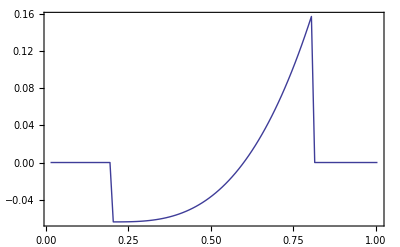

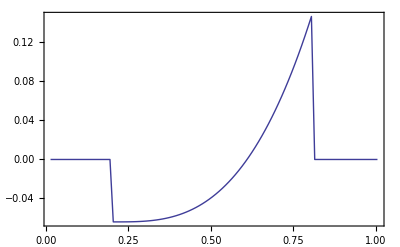

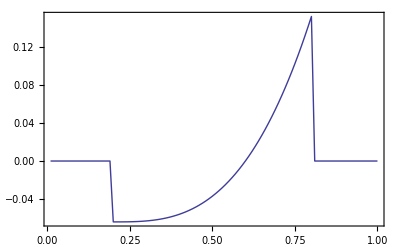

```mathematica
ϵ=10^-6;NN=100;dx=1/NN;
ListLinePlot[Table[{(i+1/2) dx,un[i]},{i,1,NN}],Frame->True,Axes->False,PlotRange->All]
ListLinePlot[Table[{(i+1/2)  dx,up[i]},{i,1,NN}],Frame->True,Axes->False,PlotRange->All]
ListLinePlot[Table[{i  dx,u[i  dx]},{i,1,NN}],Frame->True,Axes->False,PlotRange->All]
Clear[ϵ,dx,NN]
```